# Reconstructing a Model for Gravity at Large Distances from Dark Matter Density Profiles (Numerical Analysis and Construction Figures File)

```mathematica
Figure 1 -Effective Potential
```

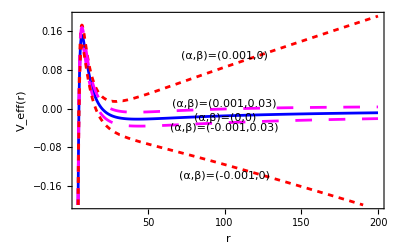

fig1.pdf

-(l^2 m)/r^3+l^2/(2 r^2)+(a l^2-m)/r-4/3 (a b l^2)+(a+3/2 a b^2 l^2) r+(-(4 a b)/3-8/5 a b^3 l^2) r^2+((3 a b^2)/2+5/3 a b^4 l^2) r^3+O[r]^4

```mathematica
(* Plot of the effective potential eq. (4.13) that determines the velocity rotation curves for values l=10, M=2 *)
rmax=200;
ll=10;
mm=2.;
aa=0.000;
bb=0.00000001;
veff3[r_,mm_,l_,aa_,bb_]:=-mm/r+l^2/(2  r^2)-(mm   l^2)/r^3-(2 aa)/(bb^2   r)(1-1/(1+bb  r)-Log[1+bb  r])(1+l^2/r^2) 
vpl1=Plot[veff3[r,mm,ll,aa,bb],{r,0.3,rmax},PlotStyle->{RGBColor[0,0,1],Thickness[0.005]},Frame->True,PlotRange->{-0.2,0.2}];
ll=10;
mm=2.;
aa=0.001;
bb=0.00000001;
vpl2=Plot[veff3[r,mm,ll,aa,bb],{r,0.3,rmax},PlotStyle->{RGBColor[1,0,0],Dashing[0.01], Thickness[0.005]},Frame->True,PlotRange->{-0.2,0.2}];
ll=10;
mm=2.;
aa=0.001;
bb=0.03;
vpl3=Plot[veff3[r,mm,ll,aa,bb],{r,0.3,rmax},PlotStyle->{RGBColor[1,0,1],Dashing[0.03], Thickness[0.005]},Frame->True,PlotRange->{-0.2,0.2}];
ll=10;
mm=2.;
aa=-0.001;
bb=0.03;
vpl4=Plot[veff3[r,mm,ll,aa,bb],{r,0.3,rmax},PlotStyle->{RGBColor[1,0,1],Dashing[0.03], Thickness[0.005]},Frame->True,PlotRange->{-0.2,0.2}];
ll=10;
mm=2.;
aa=-0.001;
bb=0.00000001;
vpl5=Plot[veff3[r,mm,ll,aa,bb],{r,0.3,rmax},PlotStyle->{RGBColor[1,0,0],Dashing[0.01], Thickness[0.005]},Frame->True,PlotRange->{-0.2,0.2}];
fig1=Show[vpl1,vpl2,vpl3,vpl4,vpl5,
Graphics[{Inset["(α,β)=(0.001,0)",{100,0.11},BaseStyle->Directive[Small,Bold,Italic]]}],
Graphics[{Inset["(α,β)=(0.001,0.03)",{100,0.01},BaseStyle->Directive[Small,Bold,Italic]]}],
Graphics[{Inset["(α,β)=(0,0)",{100,-0.02},BaseStyle->Directive[Small,Bold,Italic]]}],
Graphics[{Inset["(α,β)=(-0.001,0.03)",{100,-0.04},BaseStyle->Directive[Small,Bold,Italic]]}],
Graphics[{Inset["(α,β)=(-0.001,0)",{100,-0.14},BaseStyle->Directive[Small,Bold,Italic]]}],
Frame->True,Axes->True,FrameLabel->{"r","V_eff(r)"},BaseStyle->{Small,FontFamily->"Times",Italic},LabelStyle->Directive[Black,Small],PlotRange->All]
SetDirectory[NotebookDirectory[]];
Export["fig1.pdf",fig1,ImageResolution->1000]
Series[veff3[r,m,l,a,b],{r,0,3}]
```

```mathematica
Figure 2 -Best Fit Forms of  the Velocity Profiles
```

```mathematica
• Setting the directory
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
• Reconstructed Potential
```

```mathematica
(* Reconstructed potential is used to obtain the term g(r) of the metric function f(r) *)

Clear[ff,f,ρ,v,g,mm];
f[r_]:=1-g[r];
ff[r_]:=r^2;
v[r_]:=1+4 α r/(1+β r)^2
ρ[r_]:=0;
eq1=f'[r] ff'[r]+f[r] ff''[r]-2 v[r]+2ρ[r]==0 //Simplify
gg=DSolve[eq1,g,r][[1,1,2,2]] //FullSimplify
```

2 (g[r]+r ((4 α)/(1+r β)^2+g'[r]))==0

(C[1]-(4 α (1/(1+r β)+Log[1+r β]))/β^2)/r

```mathematica
Series[gg,{r,0,5}]
```

(-(4 α)/β^2+C[1])/r-2 α r+8/3 α β r^2-3 (α β^2) r^3+16/5 α β^3 r^4-10/3 (α β^4) r^5+O[r]^6

```mathematica
• Data
```

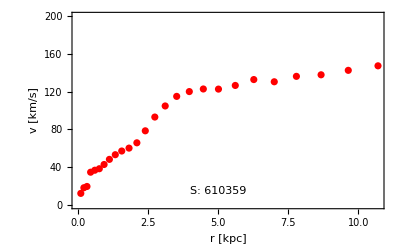

```mathematica
(* Velocity rotation data and plot of the galaxy S: 610359 (from the "S-sample" of https://www.ioa.s.u-tokyo.ac.jp/~sofue/smd2018/.) *)

datag1a={{0.1,12.24},{0.21,18.23},{0.32,19.56},{0.45,34.68},{0.6,36.78},{0.76,38.35},{0.93,42.83},{1.12,48.27},{1.33,53.21},{1.56,57.12},{1.82,60.19},{2.1,65.82},{2.4,78.52},{2.74,93.1},{3.11,104.84},{3.52,114.99},{3.97,120.08},{4.47,122.83},{5.01,122.7},{5.61,126.57},{6.27,132.81},{7.,130.47},{7.79,136.21},{8.67,137.86},{9.64,142.57},{10.7,147.36}};
datag1b=Table[{datag1a[[i,1]],datag1a[[i,2]]^2},{i,5,Length[datag1a]}];
datag1c=Table[{datag1a[[i,1]],datag1a[[i,2]]^2},{i,1,Length[datag1a]}];
ListPlot[datag1a,Frame-> True, FrameLabel->{"r [kpc]", "v [km/s]"},PlotStyle->Red,Epilog-> {Text["S: 610359",{5,15}]}, PlotRange->{0,200},BaseStyle->FontSize->12]
```

{{0.23,15361.1},{0.49,33800.8},{0.77,38177.3},{1.08,41930.8},{1.43,44457.7},{1.8,45313.6},{2.21,45130.8},{2.67,44656.1},{3.17,43793.9},{3.72,42840.7},{4.33,42193.3},{4.99,42279.6},{5.73,43405.6},{6.53,44808.4},{7.42,46302.4},{8.39,47184.5},{9.47,47284.5},{10.65,46358.4},{11.94,45232.8},{13.37,44504.1},{14.94,44285.},{16.67,45237.},{18.57,46379.9},{20.66,46911.2},{22.96,45360.5},{25.49,42411.3},{28.27,38506.2},{31.33,34954.},{34.7,33167.7}}

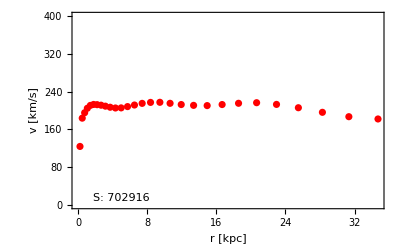

```mathematica
(* Velocity rotation data and plot of the galaxy S: 702916 (from the "S-sample" of https://www.ioa.s.u-tokyo.ac.jp/~sofue/smd2018/.) *)

datag2a={{0.23,123.94},{0.49,183.85},{0.77,195.39},{1.08,204.77},{1.43,210.85},{1.8,212.87},{2.21,212.44},{2.67,211.32},{3.17,209.27},{3.72,206.98},{4.33,205.41},{4.99,205.62},{5.73,208.34},{6.53,211.68},{7.42,215.18},{8.39,217.22},{9.47,217.45},{10.65,215.31},{11.94,212.68},{13.37,210.96},{14.94,210.44},{16.67,212.69},{18.57,215.36},{20.66,216.59},{22.96,212.98},{25.49,205.94},{28.27,196.23},{31.33,186.96},{34.7,182.12}};
datag2b=Table[{datag2a[[i,1]],datag2a[[i,2]]^2},{i,9,Length[datag2a]}];
datag2c=Table[{datag2a[[i,1]],datag2a[[i,2]]^2},{i,1,Length[datag2a]}]
ListPlot[datag2a,Frame-> True, FrameLabel->{"r [kpc]", "v [km/s]"},PlotStyle->Red,Epilog-> {Text["S: 702916",{5,15}]}, PlotRange->{0,400},BaseStyle->FontSize->12]
```

```mathematica
• Rotation Curve ( figure 2a)
```

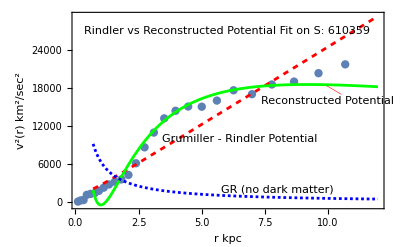

fig2a.pdf

| Estimate | Standard Error | t-Statistic | P-Value
a | 2439.16 | 112.643 | 21.6539 | 2.3572×10^-15
mm | 309.244 | 913.107 | 0.338672 | 0.738387

AdjustedRSquared | 0.959568
AIC | 411.737
BIC | 415.01
RSquared | 0.963243

| Estimate | Standard Error | t-Statistic | P-Value
a | -126456. | 4909.31 | -25.7585 | 3.06604×10^-16
b | 0.981784 | 0.0407083 | 24.1175 | 1.03366×10^-15
mm | 14527.8 | 973.912 | 14.917 | 6.06811×10^-12

AdjustedRSquared | 0.983256
AIC | 393.213
BIC | 397.577
RSquared | 0.985539

| Estimate | Standard Error | t-Statistic | P-Value
mm | 6450.06 | 4187.87 | 1.54018 | 0.138451

AdjustedRSquared | 0.0587088
AIC | 480.058
BIC | 482.24
RSquared | 0.101495

```mathematica
(* The best fit forms of the velocity profiles eq. (4.15) and eq. (4.16) on the observed halo profiles of the galaxy S: 610359 (from the "S-sample" of https://www.ioa.s.u-tokyo.ac.jp/~sofue/smd2018/.) *) 

rmin=0.7;
rmax=12;

v1[r_,a_,mm_]:=mm/r +a r
nlm1=NonlinearModelFit[datag1b,v1[r,a,mm],{a,mm},r];
pl1=ListPlot[datag1c,PlotStyle->PointSize[0.015]];
pl2=Plot[nlm1[r],{r,rmin,rmax},PlotStyle -> {RGBColor[1,0,0],Dashing[0.01],Thickness[0.005]}];

v1[r_,a_,b_,mm_]:=mm/r +(2 a (-b/(1+b r)^2+b/(1+b r)))/b^2+(2 a-2 a (1/(1+b r)+Log[1+b r]))/(b^2 r)
nlm2=NonlinearModelFit[datag1b,{v1[r,a,b,mm],{b>0}},{a,b,mm},r];
pl3=Plot[nlm2[r],{r,rmin,rmax},PlotStyle->{RGBColor[0,1,0],Thickness[0.005]}];

v1[r_,mm_]:=mm/r ;
nlm3=NonlinearModelFit[datag1b,v1[r,mm],{mm},r];
pl4=Plot[nlm3[r],{r,rmin,rmax},PlotStyle -> {RGBColor[0,0,1],Dashing[0.005],Thickness[0.005]},PlotRange->All];

fig2a=Show[pl1,pl2,pl3,pl4,
Graphics[{Inset["Rindler vs Reconstructed Potential Fit on S: 610359",{6,27000},BaseStyle->Directive[Small,Bold,Italic]]}],
Graphics[{Inset["GR (no dark matter)",{8,2000},BaseStyle->Directive[Small,Italic]]}],
Graphics[{Inset["Grumiller - Rindler Potential",{6.5,10000},BaseStyle->Directive[Small,Italic]]}],
Graphics[{Inset["Reconstructed Potential",{10,16000},BaseStyle->Directive[Small,Italic]]}],
Graphics[{Thickness[0.001],Red,Line[{{10.549038337212307,16990.314960022944},{9.964929208688906,18352.386527881317}}]}],
Frame->True,PlotRange->All,Axes->False,FrameLabel->{"r kpc","v^2(r) km^2/sec^2"},BaseStyle->{Small,FontFamily->"Times",Italic},LabelStyle->Directive[Black,Small],Axes->False]
Export["fig2a.pdf",fig2a,ImageResolution->1000]
nlm1["ParameterTable"]
Grid[Transpose[{#,nlm1[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]
nlm2["ParameterTable"]
Grid[Transpose[{#,nlm2[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]
nlm3["ParameterTable"]
Grid[Transpose[{#,nlm3[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]
```

```mathematica
• Rotation Curve ( figure 2b)
```

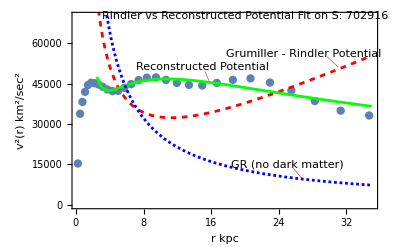

fig2b.pdf

| Estimate | Standard Error | t-Statistic | P-Value
a | 1432.13 | 169.23 | 8.46265 | 7.19945×10^-8
mm | 182574. | 21011.1 | 8.68942 | 4.80632×10^-8

AdjustedRSquared | 0.922811
AIC | 458.43
BIC | 461.564
RSquared | 0.930162

| Estimate | Standard Error | t-Statistic | P-Value
a | -147746. | 11733.6 | -12.5917 | 2.31638×10^-10
b | 0.55487 | 0.0361188 | 15.3624 | 8.63992×10^-12
mm | 165383. | 11972.7 | 13.8134 | 5.07617×10^-11

AdjustedRSquared | 0.998052
AIC | 382.031
BIC | 386.209
RSquared | 0.99833

| Estimate | Standard Error | t-Statistic | P-Value
mm | 257019. | 40615. | 6.32819 | 3.54835×10^-6

AdjustedRSquared | 0.650268
AIC | 489.236
BIC | 491.325
RSquared | 0.666922

```mathematica
(* The best fit forms of the velocity profiles eq. (4.15) and eq. (4.16) on the observed halo profiles of the galaxy S: 610359 (from the "S-sample" of https://www.ioa.s.u-tokyo.ac.jp/~sofue/smd2018/.) *) 

rmin=2.5;
rmax=35;

v1[r_,a_,mm_]:=mm/r +a r
nlm1=NonlinearModelFit[datag2b,v1[r,a,mm],{a,mm},r];
pl1=ListPlot[datag2c,PlotStyle->PointSize[0.015]];
pl2=Plot[nlm1[r],{r,rmin,rmax},PlotStyle -> {RGBColor[1,0,0],Dashing[0.01],Thickness[0.005]}];

v1[r_,a_,b_,mm_]:=mm/r +(2 a (-b/(1+b r)^2+b/(1+b r)))/b^2+(2 a-2 a (1/(1+b r)+Log[1+b r]))/(b^2 r)
nlm2=NonlinearModelFit[datag2b,{v1[r,a,b,mm],{b>0}},{a,b,mm},r];
pl3=Plot[nlm2[r],{r,rmin,rmax},PlotStyle->{RGBColor[0,1,0],Thickness[0.005]}];

v1[r_,mm_]:=mm/r ;
nlm3=NonlinearModelFit[datag2b,v1[r,mm],{mm},r];
pl4=Plot[nlm3[r],{r,rmin,rmax},PlotStyle -> {RGBColor[0,0,1],Dashing[0.005],Thickness[0.005]},PlotRange->All];

fig2b=Show[pl1,pl2,pl3,pl4,
Graphics[{Inset["Rindler vs Reconstructed Potential Fit on S: 702916",{20,70000},BaseStyle->Directive[Small,Bold,Italic]]}],
Graphics[{Inset["GR (no dark matter)",{25,15000},BaseStyle->Directive[Small,Italic]]}],
Graphics[{Inset["Grumiller - Rindler Potential",{27,56000},BaseStyle->Directive[Small,Italic]]}],
Graphics[{Inset["Reconstructed Potential",{15,51000},BaseStyle->Directive[Small,Italic]]}],
Graphics[{Thickness[0.001],Red,Line[{{29.725565532289803,54946.119061047924},{31.030745687572637,51140.10901921734}}]}],
Graphics[{Thickness[0.001],Red,Line[{{15.268185350695333,49474.97962591646},{15.770177718111803,45906.8452117003}}]}],
Graphics[{Thickness[0.001],Red,Line[{{25.73131394537004,13603.376623820252},{26.733604877120747,9797.691488005294}}]}],
Frame->True,Axes->False,FrameLabel->{"r kpc","v^2(r) km^2/sec^2"},BaseStyle->{Small,FontFamily->"Times",Italic},LabelStyle->Directive[Black,Small],PlotRange->{0,70000}]
Export["fig2b.pdf",fig2b,ImageResolution->1000]
nlm1["ParameterTable"]
Grid[Transpose[{#,nlm1[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]
nlm2["ParameterTable"]
Grid[Transpose[{#,nlm2[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]
nlm3["ParameterTable"]
Grid[Transpose[{#,nlm3[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]
```